# Night 5 Part 1

## 3

Find Mass:

```mathematica
N[Integrate[200*Sqrt[1-((x^2)/17)], {x, 0, Sqrt[17]}]]
```

647.656

Trying to solve in a way that makes Mathematica freak out:

```mathematica
N[Solve[Integrate[200*Sqrt[1-((x^2)/17)], {x, 0, c}]==%/2,{c}]]
```

$Aborted

Another attempt

```mathematica
Solve[Integrate[1-200*Sqrt[1-((x^2)/17)], {x, 0, c}]==%/2]
```

{{c→-17/((300 √17+1275 √17 ArcTan[4]+√(1525087+13005000 ArcTan[4]+27635625 ArcTan[4]^2))^(1/3))-(300 √17+1275 √17 ArcTan[4]+√(1525087+13005000 ArcTan[4]+27635625 ArcTan[4]^2))^(1/3)},{c→(17 (1+ⅈ √3))/(2 (300 √17+1275 √17 ArcTan[4]+√(1525087+13005000 ArcTan[4]+27635625 ArcTan[4]^2))^(1/3))+1/2 (1-ⅈ √3) (300 √17+1275 √17 ArcTan[4]+√(1525087+13005000 ArcTan[4]+27635625 ArcTan[4]^2))^(1/3)},{c→(17 (1-ⅈ √3))/(2 (300 √17+1275 √17 ArcTan[4]+√(1525087+13005000 ArcTan[4]+27635625 ArcTan[4]^2))^(1/3))+1/2 (1+ⅈ √3) (300 √17+1275 √17 ArcTan[4]+√(1525087+13005000 ArcTan[4]+27635625 ArcTan[4]^2))^(1/3)}}

```mathematica
N[%]
```

{{c→-26.0824},{c→13.0412-21.4294 ⅈ},{c→13.0412+21.4294 ⅈ}}

I am going to take a random guess and say that the center of lift is probably not at -26 meters.

Finding just the integral (Mathematica can do this)

```mathematica
200*Integrate[Sqrt[1-(1/17)*(x^2)], x]
```

(100 (x √(17-x^2)+17 ArcSin[x/(√17)]))/(√17)

Solving for the bottom limit which is 0. The answer is 0, so we don’t have to worry about it.

```mathematica
(100 (0 √(17-0^2)+17 ArcSin[0/(√17)]))/(√17)
```

0

Trying to solve for the top limit. Mathematica does not like me doing this.

```mathematica
Solve[(100 (c √(17-c^2)+17 ArcSin[c/(√17)]))/(√17)==321.835]
```

$Aborted

This takes too long and makes my computer sound like it is about to prepare for takeoff so it does not work.

Ok, time to solve this in a really stupid way. Here is a graph of the function but slightly simplified. Now, I am looking for where the function is equal to 13.35. But for some reason Mathematica won’t do it for me so...

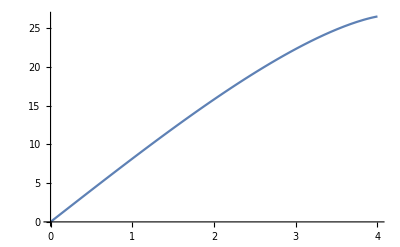

```mathematica
Plot[c √(17-c^2)+17 ArcSin[c/(√17)], {c, 0, 4}]
```

Here is the same graph zoomed in so that I can get close enough to the answer. I told you it would be really stupid.

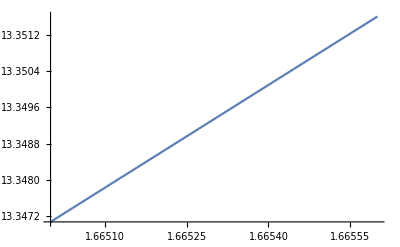

```mathematica
Plot[c √(17-c^2)+17 ArcSin[c/(√17)], {c, 1.665, 1.6656}]
```

c=1.665